## Author: Sreenath K. Manikandan, Nordita, KTH Royal Institute of Technology and Stockholm University

## Steady state of the quantum clock with athermal resources

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];KroneckerProduct[{{1/Sqrt[2]},{0},{-1/Sqrt[2]}},{1/Sqrt[2],0,-1/Sqrt[2]}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;g0=4;dt=0.01;gamma=3;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<10000+1,n++,rho[0]=r0;
rho[n+1]=(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gw(Lw.rho[n].Lwd-1/2(rho[n].Lwd.Lw+Lwd.Lw.rho[n]))+g0(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))));]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;g0=4;dt=0.01;gamma=3;oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<10000+1,n++,rho1[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
rho1[n+1]=Mg0.(M0.(rho1[n]+dt(-I (H0.rho1[n]-rho1[n].H0)-gamma(oX.(oX.rho1[n]-rho1[n].oX)-(oX.rho1[n]-rho1[n].oX).oX))).Transpose[M0]).Transpose[Mg0]+Mg1.(M0.(rho1[n]+dt(-I (H0.rho1[n]-rho1[n].H0)-gamma(oX.(oX.rho1[n]-rho1[n].oX)-(oX.rho1[n]-rho1[n].oX).oX))).Transpose[M0]).Transpose[Mg1]+Mg0.(M1.(rho1[n]+dt(-I (H0.rho1[n]-rho1[n].H0)-gamma(oX.(oX.rho1[n]-rho1[n].oX)-(oX.rho1[n]-rho1[n].oX).oX))).Transpose[M1]).Transpose[Mg0]+Mg1.(M1.(rho1[n]+dt(-I (H0.rho1[n]-rho1[n].H0)-gamma(oX.(oX.rho1[n]-rho1[n].oX)-(oX.rho1[n]-rho1[n].oX).oX))).Transpose[M1]).Transpose[Mg1];]
```

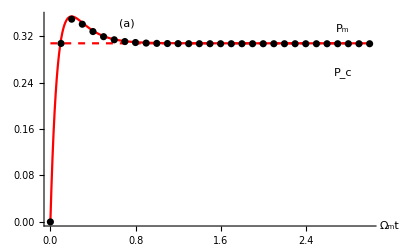

```mathematica
pmm=Show[Plot[(2 g0 gamma (8 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(gw (8 gamma+gw) (6 g0 gamma+(g0+gamma) gw)+4 (2 g0 gamma+(g0+gamma) gw) Ω^2+gamma ((2 g0-gw) gw (8 gamma+gw)-4 (2 g0+gw) Ω^2) Cos[2 theta]),{n,0, 300 dt},PlotStyle->{Red,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]},Epilog->{{Style[Text["P_m",Scaled[{0.9,0.92}]],16,Red]},{Style[Text["(a)",Scaled[{0.25,0.95}]],16,Black]},{Style[Text["P_c",Scaled[{0.9,0.72}]],16,Blue]}}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Red}],ListPlot[{Table[{ n dt,Tr[rho1[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

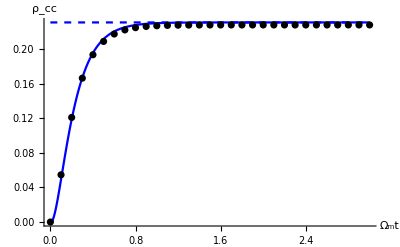

```mathematica
pcc=Show[Plot[-(2 gamma gw (8 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(-gw (8 gamma+gw) (6 g0 gamma+(g0+gamma) gw)-4 (2 g0 gamma+(g0+gamma) gw) Ω^2+gamma (-(2 g0-gw) gw (8 gamma+gw)+4 (2 g0+gw) Ω^2) Cos[2 theta]),{n,0,300 dt},PlotStyle->{Blue,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black],Style["ρ_cc",Italic,24,Black]}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Blue}],ListPlot[{Table[{ n dt,Tr[rho1[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

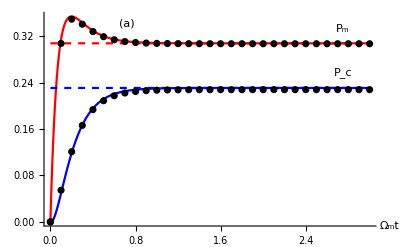

```mathematica
pad=Show[pmm,pcc]
```

```mathematica
gw=3;gamma=.;g0=4;t4=Table[{gamma,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M0]]],1-Chop[Tr[M0.(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=Mg0.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg0]+Mg1.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg1];
];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gamma,1,10,1}]
```

```mathematica
t4={{1,0.007193806193806195,0.007145304695304696},{2,0.008722277722277724,0.00865011788211788},{3,0.009501498501498503,0.009415080919080918},{4,0.009964035964035965,0.009868717282717283},{5,0.010112887112887114,0.010014965034965033},{6,0.010413586413586414,0.010309712287712287},{7,0.010428571428571428,0.01032424775224775},{8,0.01066133866133866,0.010551792207792208},{9,0.0106983016983017,0.010587952047952048},{10,0.010776223776223776,0.010664355644355644}};
```

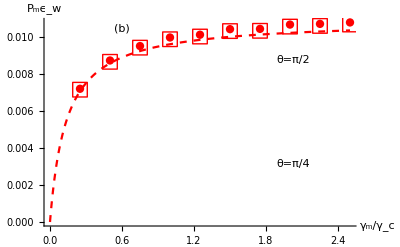

```mathematica
theta=Pi/2;pwa=Show[Plot[(gw (2 g0 g0 gamma (8 g0 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(gw (8 g0 gamma+gw) (6 g0 g0 gamma+(g0+g0 gamma) gw)+4 (2 g0 g0 gamma+(g0+g0 gamma) gw) Ω^2+g0 gamma ((2 g0-gw) gw (8 g0 gamma+gw)-4 (2 g0+gw) Ω^2) Cos[2 theta])dt),{gamma,0,10/g0},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,Epilog->{{Style[Text["θ=π/2",Scaled[{0.8,0.8}]],16,Red]},{Style[Text["(b)",Scaled[{0.25,0.95}]],16,Black]},{Style[Text["θ=π/4",Scaled[{0.8,0.3}]],16,Blue]}}],ListPlot[Table[{t4[[i]][[1]]/g0,t4[[i]][[2]]},{i,1,Length[t4]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{t4[[i]][[1]]/g0,t4[[i]][[3]]},{i,1,Length[t4]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
gw=3;gamma=.;g0=4;theta=Pi/4;oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];t42=Table[{gamma,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M0]]],1-Chop[Tr[M0.(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=Mg0.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg0]+Mg1.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg1];
];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gamma,1,10,1}]
```

```mathematica
t42={{1,0.0032657342657342655,0.0032556203796203793},{2,0.003852147852147852,0.00383764035964036},{3,0.004146853146853147,0.004130015984015983},{4,0.004211788211788212,0.004194549450549451},{5,0.004284715284715285,0.004267036963036963},{6,0.004374625374625375,0.004355824175824177},{7,0.004372627372627373,0.004353710289710289},{8,0.004455544455544455,0.004435832167832167},{9,0.004500499500499501,0.004480427572427573},{10,0.00439060939060939,0.004371832167832167}};
```

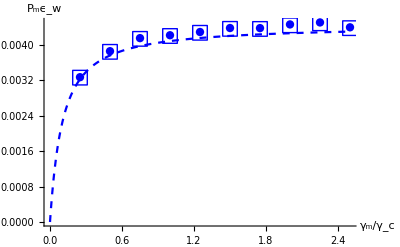

```mathematica
theta=Pi/4;pwb=Show[Plot[(gw (2 g0 g0 gamma (8 g0 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(gw (8 g0 gamma+gw) (6 g0 g0 gamma+(g0+g0 gamma) gw)+4 (2 g0 g0 gamma+(g0+g0 gamma) gw) Ω^2+g0 gamma ((2 g0-gw) gw (8 g0 gamma+gw)-4 (2 g0+gw) Ω^2) Cos[2 theta])dt),{gamma,0,10/g0},PlotStyle->{Blue,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All],ListPlot[Table[{t42[[i]][[1]]/g0,t42[[i]][[2]]},{i,1,Length[t42]}],PlotStyle->{Blue,PointSize[0.015]}],ListPlot[Table[{t42[[i]][[1]]/g0,t42[[i]][[3]]},{i,1,Length[t42]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

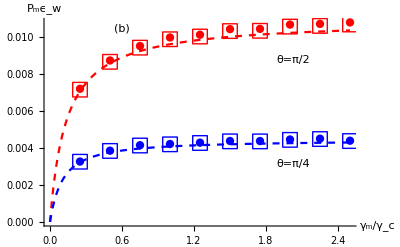

```mathematica
pat=Show[pwa,pwb]
```

```mathematica
gw=3;gamma=.;g0=4;theta=Pi/3;oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];t43=Table[{gamma,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],1-Chop[Tr[M0.rho[n].M0]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=Mg0.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg0]+Mg1.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg1];
];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gamma,1,10,1}]
```

```mathematica
t43={{1,0.005008991008991008,0.004985288711288712},{2,0.006140859140859142,0.006104789210789212},{3,0.006409590409590409,0.006369966033966035},{4,0.006691308691308692,0.006647726273726276},{5,0.006886113886113886,0.006839888111888112},{6,0.0068481518481518485,0.006802643356643358},{7,0.0071098901098901116,0.00706112087912088},{8,0.007060939060939062,0.007012473526473526},{9,0.007168831168831168,0.007118557442557444},{10,0.007121878121878122,0.007072571428571428}};
```

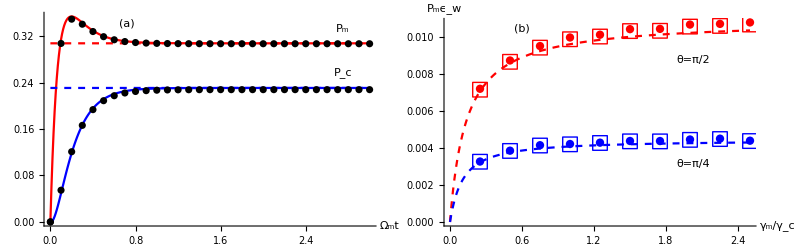

```mathematica
GraphicsGrid[{{pad,pat}},Spacings->{0, 0},ImageSize->800]
```

## Simulations for hybrid quantum clocks

```mathematica
fm[theta_]:=-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

```mathematica
fmt[theta_,betah_,gamma_,gw_]:=-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

```mathematica
fc[theta_]:=-((-ⅇ^(3 betac ω) gammah^3 gw-ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+gammah+3 gw)+ⅇ^(betac ω) gw (13 gamma+2 (gammah+gw)))-ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 (gamma+gammah)+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+7 gamma (gammah+2 gw)+(gammah+gw) (gammah+2 gw))+ⅇ^(2 betac ω) gw ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(3 betah Ω) (-gammac^3 (gamma+gammah+gw)-ⅇ^(betac ω) gammac^2 (8 gamma^2+2 (gammah+gw)^2+gamma (14 gammah+15 gw))-ⅇ^(3 betac ω) gamma gw ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2)-ⅇ^(2 betac ω) gammac ((gammah+gw)^3+8 gamma^2 (5 gammah+6 gw)+gamma (gammah+gw) (13 gammah+15 gw)+4 gamma Ω^2+4 (gammah+gw) Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (2 gammah-ⅇ^(betah Ω) (-8 gamma+2 gammah+gw))+ⅇ^(2 betac ω) gammac (gammah^2-2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)-ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) gw (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

```mathematica
fct[theta_,betah_,gamma_,gw_]:=-((-ⅇ^(3 betac ω) gammah^3 gw-ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+gammah+3 gw)+ⅇ^(betac ω) gw (13 gamma+2 (gammah+gw)))-ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 (gamma+gammah)+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+7 gamma (gammah+2 gw)+(gammah+gw) (gammah+2 gw))+ⅇ^(2 betac ω) gw ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(3 betah Ω) (-gammac^3 (gamma+gammah+gw)-ⅇ^(betac ω) gammac^2 (8 gamma^2+2 (gammah+gw)^2+gamma (14 gammah+15 gw))-ⅇ^(3 betac ω) gamma gw ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2)-ⅇ^(2 betac ω) gammac ((gammah+gw)^3+8 gamma^2 (5 gammah+6 gw)+gamma (gammah+gw) (13 gammah+15 gw)+4 gamma Ω^2+4 (gammah+gw) Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (2 gammah-ⅇ^(betah Ω) (-8 gamma+2 gammah+gw))+ⅇ^(2 betac ω) gammac (gammah^2-2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)-ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) gw (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;
Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
rho[n+1]=(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])+(M1.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M1]);]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<1000+1,n++,rho2[0]=r0;
rho2[n+1]=(rho2[n]+dt (-I (H0.rho2[n]-rho2[n].H0)-gamma (oX.(oX.rho2[n]-rho2[n].oX)-(oX.rho2[n]-rho2[n].oX).oX)+gammah(Lh.rho2[n].Lhd-1/2(rho2[n].Lhd.Lh+Lhd.Lh.rho2[n]))+gammah Exp[-betah Ω ](Lhd.rho2[n].Lh-1/2(rho2[n].Lh.Lhd+Lh.Lhd.rho2[n]))+gw(Lw.rho2[n].Lwd-1/2(rho2[n].Lwd.Lw+Lwd.Lw.rho2[n]))+gammac(Lc.rho2[n].Lcd-1/2(rho2[n].Lcd.Lc+Lcd.Lc.rho2[n]))+gammac Exp[-betac ω ](Lcd.rho2[n].Lc-1/2(rho2[n].Lc.Lcd+Lc.Lcd.rho2[n]))));]
```

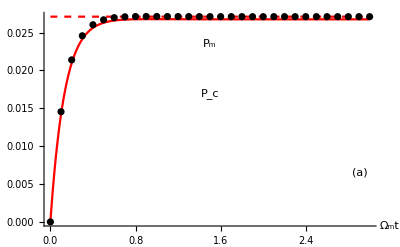

```mathematica
pmmt=Show[Plot[fm[theta],{n,0, 300 dt},PlotStyle->{Red,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]},Epilog->{{Style[Text["P_m",Scaled[{0.5,0.85}]],16,Red]},{Style[Text["(a)",Scaled[{0.95,0.25}]],16,Black]},{Style[Text["P_c",Scaled[{0.5,0.62}]],16,Blue]}}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Red}],ListPlot[{Table[{ n dt,Tr[rho2[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

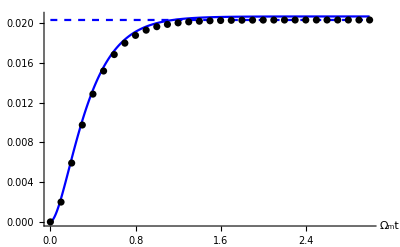

```mathematica
pcct=Show[Plot[fc[theta],{n,0, 300 dt},PlotStyle->{Blue,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Blue}],ListPlot[{Table[{ n dt,Tr[rho2[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

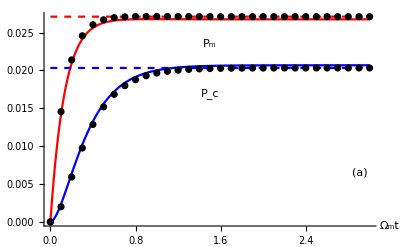

```mathematica
pta=Show[pmmt,pcct]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/4;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;
Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
rho[n+1]=(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])+(M1.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M1]);]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/4;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<1000+1,n++,rho2[0]=r0;
rho2[n+1]=(rho2[n]+dt (-I (H0.rho2[n]-rho2[n].H0)-gamma (oX.(oX.rho2[n]-rho2[n].oX)-(oX.rho2[n]-rho2[n].oX).oX)+gammah(Lh.rho2[n].Lhd-1/2(rho2[n].Lhd.Lh+Lhd.Lh.rho2[n]))+gammah Exp[-betah Ω ](Lhd.rho2[n].Lh-1/2(rho2[n].Lh.Lhd+Lh.Lhd.rho2[n]))+gw(Lw.rho2[n].Lwd-1/2(rho2[n].Lwd.Lw+Lwd.Lw.rho2[n]))+gammac(Lc.rho2[n].Lcd-1/2(rho2[n].Lcd.Lc+Lcd.Lc.rho2[n]))+gammac Exp[-betac ω ](Lcd.rho2[n].Lc-1/2(rho2[n].Lc.Lcd+Lc.Lcd.rho2[n]))));]
```

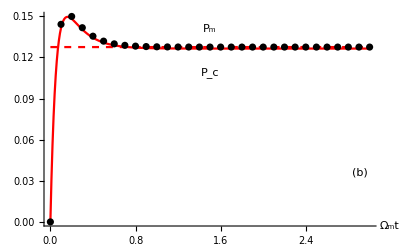

```mathematica
pmmtb=Show[Plot[fm[theta],{n,0, 300 dt},PlotStyle->{Red,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]},Epilog->{{Style[Text["P_m",Scaled[{0.5,0.92}]],16,Red]},{Style[Text["(b)",Scaled[{0.95,0.25}]],16,Black]},{Style[Text["P_c",Scaled[{0.5,0.72}]],16,Blue]}}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Red}],ListPlot[{Table[{ n dt,Tr[rho2[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

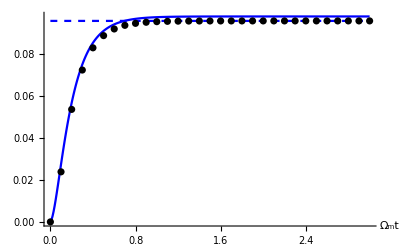

```mathematica
pcctb=Show[Plot[fc[theta],{n,0, 300 dt},PlotStyle->{Blue,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Blue}],ListPlot[{Table[{ n dt,Tr[rho2[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

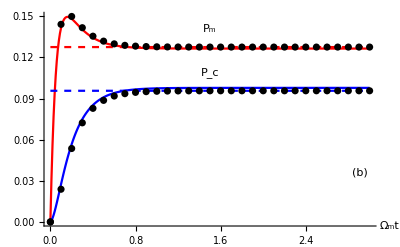

```mathematica
ptb=Show[pmmtb,pcctb]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;dt=0.01;gamma=.;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
ta3=Table[{gamma,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]],Max[0,1-Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gamma,1,10,1}]
```

{{1,0.00530869,0.00528204},{2,0.006998,0.00695165},{3,0.00798701,0.00792603},{4,0.00854545,0.00847553},{5,0.00896404,0.00888735},{6,0.0092967,0.00921384},{7,0.00957942,0.00949116},{8,0.00972228,0.00963146},{9,0.00983117,0.00973853},{10,0.0100759,0.00997843}}

```mathematica
fm1[gamma_,theta_]:=-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

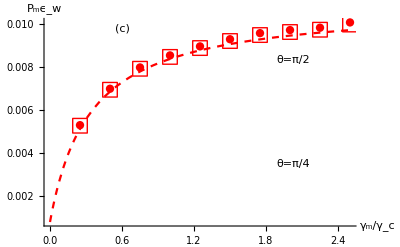

```mathematica
theta=Pi/2;pwa=Show[Plot[(gw fm1[g0 gamma,theta]dt),{gamma,0,10/g0},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0},Epilog->{{Style[Text["θ=π/2",Scaled[{0.8,0.8}]],16,Red]},{Style[Text["(c)",Scaled[{0.25,0.95}]],16,Black]},{Style[Text["θ=π/4",Scaled[{0.8,0.3}]],16,Blue]}}],ListPlot[Table[{ta3[[i]][[1]]/g0,ta3[[i]][[2]]},{i,1,Length[ta3]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{ta3[[i]][[1]]/g0,ta3[[i]][[3]]},{i,1,Length[ta3]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;dt=0.01;gamma=3;gammah=.;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
ta31=Table[{gammah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]],Max[0,1-Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gammah,1,10,1}]
```

{{1,0.00906993,0.00899145},{2,0.00867033,0.0085986},{3,0.00830869,0.00824323},{4,0.0078951,0.00783554},{5,0.00773427,0.00767683},{6,0.00734565,0.00729408},{7,0.00713686,0.00708835},{8,0.00700699,0.00696035},{9,0.00676024,0.00671646},{10,0.00655544,0.00651429}}

```mathematica
fmh[gammah_,theta_]:=-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

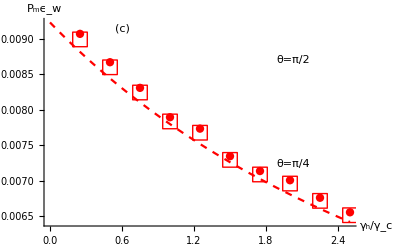

```mathematica
theta=Pi/2;pwh1=Show[Plot[(gw fmh[g0 gammah,theta]dt),{gammah,0,10/g0},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_h/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0},Epilog->{{Style[Text["θ=π/2",Scaled[{0.8,0.8}]],16,Red]},{Style[Text["(c)",Scaled[{0.25,0.95}]],16,Black]},{Style[Text["θ=π/4",Scaled[{0.8,0.3}]],16,Blue]}}],ListPlot[Table[{ta31[[i]][[1]]/g0,ta31[[i]][[2]]},{i,1,Length[ta31]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{ta31[[i]][[1]]/g0,ta31[[i]][[3]]},{i,1,Length[ta31]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/4;phi=0;gw=3;dt=0.01;gamma=3;gammah=.;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
ta32=Table[{gammah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]],Max[0,1-Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gammah,1,10,1}]
```

```mathematica
ta32={{1,0.0040589410589410594,0.004043010989010989},{2,0.00396003996003996,0.003945150849150849},{3,0.003968031968031967,0.003952883116883118},{4,0.003924075924075924,0.003909472527472527},{5,0.003891108891108891,0.0038767332667332664},{6,0.003708291708291709,0.003695316683316683},{7,0.0036633366633366635,0.0036506573426573425},{8,0.003601398601398601,0.003589058941058941},{9,0.003551448551448551,0.0035395224775224775},{10,0.003475524475524475,0.0034640119880119877}};
```

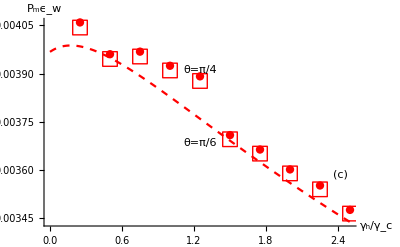

```mathematica
theta=Pi/4;pwh2=Show[Plot[(gw fmh[g0 gammah,theta]dt),{gammah,0,10/g0},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_h/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0},Epilog->{{Style[Text["θ=π/4",Scaled[{0.5,0.75}]],16,Red]},{Style[Text["(c)",Scaled[{0.95,0.25}]],16,Black]},{Style[Text["θ=π/6",Scaled[{0.5,0.4}]],16,Blue]}}],ListPlot[Table[{ta32[[i]][[1]]/g0,ta32[[i]][[2]]},{i,1,Length[ta32]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{ta32[[i]][[1]]/g0,ta32[[i]][[3]]},{i,1,Length[ta32]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/6;phi=0;gw=3;dt=0.01;gamma=3;gammah=.;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
ta31=Table[{gammah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]],Max[0,1-Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gammah,1,10,1}]
```

```mathematica
ta33={{1,0.0021308691308691303,0.002126483516483516},{2,0.002243756243756243,0.0022388911088911077},{3,0.002294705294705294,0.002289596403596403},{4,0.0022747252747252747,0.002269672327672327},{5,0.002299700299700299,0.002294545454545454},{6,0.0022587412587412583,0.002253954045954045},{7,0.002204795204795204,0.0022002277722277712},{8,0.0022667332667332665,0.0022617942057942047},{9,0.0022137862137862133,0.00220920879120879},{10,0.002227772227772227,0.0022230269730269723}};
```

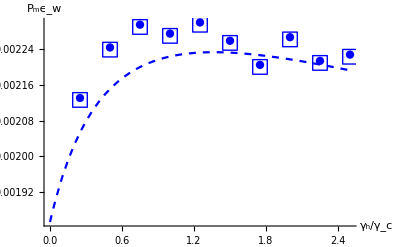

```mathematica
theta=Pi/6;pwh3=Show[Plot[(gw fmh[g0 gammah,theta]dt),{gammah,0,10/g0},PlotStyle->{Blue,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_h/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0}],ListPlot[Table[{ta33[[i]][[1]]/g0,ta33[[i]][[2]]},{i,1,Length[ta33]}],PlotStyle->{Blue,PointSize[0.015]}],ListPlot[Table[{ta33[[i]][[1]]/g0,ta33[[i]][[3]]},{i,1,Length[ta33]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

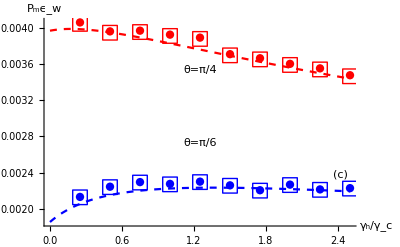

```mathematica
g3=Show[pwh2,pwh3]
```

## Thermal comparison

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=.;betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
tat=Table[{betah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]],Max[0,1-Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{betah,0,10,1}]
```

{{0,0.0101818,0.0100826},{1,0.00885115,0.00877638},{2,0.00818182,0.00811754},{3,0.00792108,0.00786133},{4,0.00784515,0.00778634},{5,0.00784316,0.00778441},{6,0.00767632,0.00762028},{7,0.00787612,0.00781734},{8,0.0077982,0.00774051},{9,0.00788911,0.00782994},{10,0.00771728,0.00766062}}

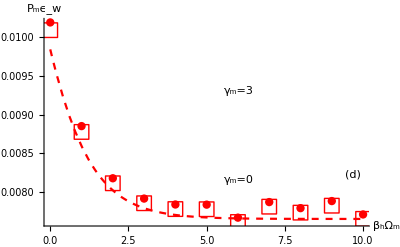

```mathematica
theta=Pi/2;pwh34=Show[Plot[(gw fmt[Pi/2,b,3,3]dt),{b,0,10},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["β_hΩ_m",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0},Epilog->{{Style[Text["γ_m=3",Scaled[{0.6,0.65}]],16,Red]},{Style[Text["(d)",Scaled[{0.95,0.25}]],16,Black]},{Style[Text["γ_m=0",Scaled[{0.6,0.22}]],16,Blue]}}],ListPlot[Table[{tat[[i]][[1]],tat[[i]][[2]]},{i,1,Length[tat]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{tat[[i]][[1]],tat[[i]][[3]]},{i,1,Length[tat]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;dt=0.01;gamma=0;gammah=4;gammac=4;
g0=4;betah=.;betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
tat1=Table[{betah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]],Max[0,1-Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{betah,0,10,1}]
```

{{0,0.00868432,0.00861314},{1,0.00474326,0.00472203},{2,0.00202697,0.00202315},{3,0.000815185,0.000814669},{4,0.000313686,0.000313596},{5,0.000105894,0.000105884},{6,0.000041958,0.000041952},{7,0.000022977,0.000022977},{8,8.99101×10^-6,8.99101×10^-6},{9,9.99001×10^-7,9.99001×10^-7},{10,9.99001×10^-7,9.99001×10^-7}}

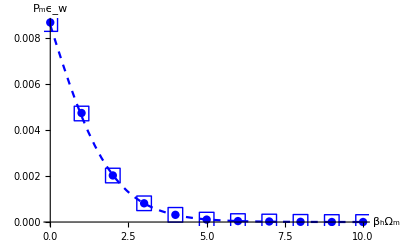

```mathematica
theta=Pi/2;pwh4=Show[Plot[(gw fmt[Pi/2,b,0,3]dt),{b,0,10},PlotStyle->{Blue,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["β_hΩ_m",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0}],ListPlot[Table[{tat1[[i]][[1]],tat1[[i]][[2]]},{i,1,Length[tat1]}],PlotStyle->{Blue,PointSize[0.015]}],ListPlot[Table[{tat1[[i]][[1]],tat1[[i]][[3]]},{i,1,Length[tat1]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

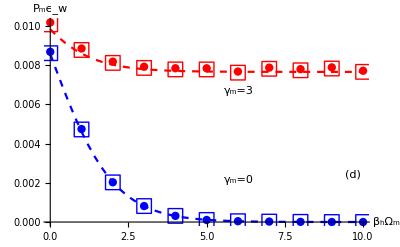

```mathematica
g4=Show[pwh34,pwh4]
```

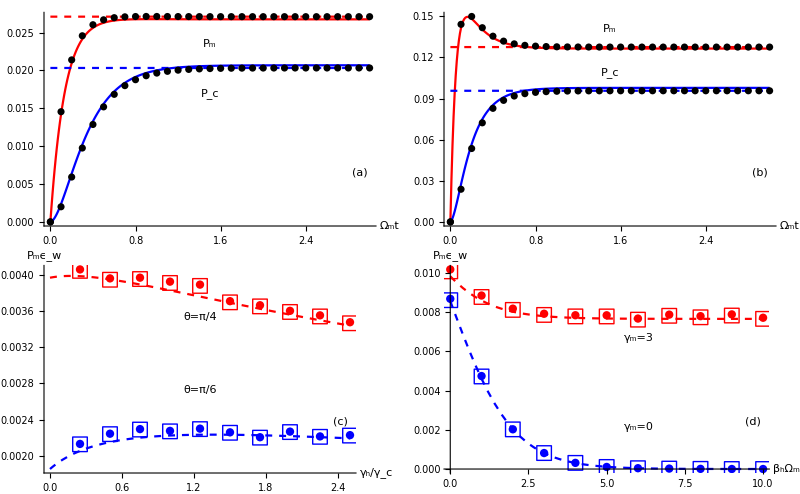

```mathematica
GraphicsGrid[{{pta,ptb},{g3,g4}},Spacings->{0, 0},ImageSize->800]
```